```mathematica
(* Liquid-vapour phase transition curve findings .... *)
```

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=300},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[MonteCarloSum[n,P,T,q,E0]]
]
```

2.31109628090263×10^1512

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
FindRoot[
MonteCarloSum[n,P,T,q,E0]==0,{{T,1000},{P,10^5}}
]
]
```

$Aborted

```mathematica
FindRoot[Sin[x]+Exp[x],{x,0}]
```

{x→-0.588533}

```mathematica
Block[
{n=500,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=300},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

1.99049×10^157

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=300},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

4.23707×10^20

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=200},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-5.54918×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^4,T=200},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-3.49473×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10,T=400},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-7.48072×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^4,T=200},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=200},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-5.43442×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=250},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

4.09026×10^20

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=225},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

3.8497×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-2.25565×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=218},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

4.06549×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=215},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

5.81232×10^20

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=213},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

2.61489×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-2.29574×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212.5},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

1.44439×10^22

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212.25},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-5.94513×10^21

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212.375},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

1.09129×10^21

```mathematica
(212.25+212.375)/2
```

212.313

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212.3125},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

1.4719×10^22

```mathematica
(212.25+212.313)/2
```

212.282

```mathematica
Block[
{n=50,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T=212.29425},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
MonteCarloSum[n,P,T,q,E0]
]
```

-9.68111×10^20

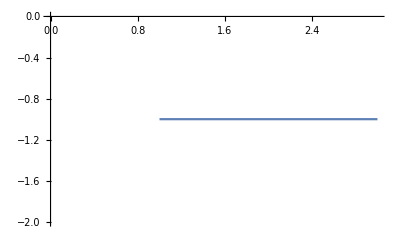

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
ListLinePlot[Table[Sign[MonteCarloSum[n,P,T,q,E0]],{T,212.25,212.35,0.05}]]
]
```

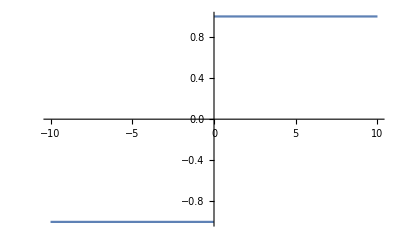

```mathematica
Plot[Sign[x],{x,-10,10}]
```

```mathematica
Sign[0]
```

0

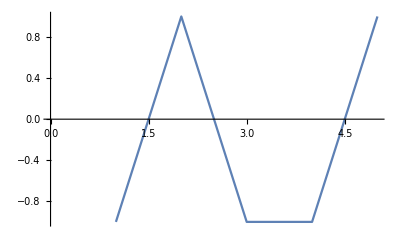

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
ListLinePlot[Table[Sign[MonteCarloSum[n,P,T,q,E0]],{T,212.25,212.35,0.025}]]
]
```

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[Table[{T,Sign[MonteCarloSum[n,P,T,q,E0]]},{T,212.25,212.35,0.025}]]
]
```

{{212.25,-1},{212.275,1},{212.3,-1},{212.325,-1},{212.35,-1}}

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[Table[{T,Sign[MonteCarloSum[n,P,T,q,E0]]},{T,212.25,212.35,0.01}]]
]
```

{{212.25,1},{212.26,-1},{212.27,1},{212.28,-1},{212.29,1},{212.3,1},{212.31,-1},{212.32,1},{212.33,1},{212.34,1},{212.35,-1}}

```mathematica
Block[
{n=5*10^3,q=1.6*10^(-19),E0=10^15,k=1.38*10^(-23),MonteCarloSum,P=10^5,T},
MonteCarloSum[n_,P_,T_,q_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/216/(k T)^2/P]+π/18 Sqrt[2 k T/P](BesselJ[1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/P](q E0 (n+s)/k/T)^(3/2)])-HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (s+n)^3/1728/(k T)^2/P]-π/36 Sqrt[k T/P](BesselJ[1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0 (n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[Table[{T,Sign[MonteCarloSum[n,P,T,q,E0]]},{T,212.25,212.35,0.005}]]
]
```

{{212.25,-1},{212.255,1},{212.26,-1},{212.265,1},{212.27,1},{212.275,1},{212.28,-1},{212.285,-1},{212.29,-1},{212.295,1},{212.3,-1},{212.305,1},{212.31,-1},{212.315,1},{212.32,1},{212.325,-1},{212.33,-1},{212.335,-1},{212.34,1},{212.345,-1},{212.35,-1}}